## Emissions scenarios within global CO2 quota

```mathematica
(* Set the working directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/yonantan_help"];
```

## Historical emissions data

```mathematica
(* Import emissions data from Yonatan spreadsheet *)
emissionsHisRaw=Import["historical carbon budget 2018 temp.xlsx"][[1]];
```

```mathematica
(* Display head of data *)
emissionsHisRaw[[1;;5]]//TableForm
```

Year | total Ct CO2
1850. | 2.71801
1851. | 2.73254
1852. | 2.7616
1853. | 2.78794

```mathematica
(* Select dates 1850-2017 (remove titles) *)
emissionsHis=emissionsHisRaw[[2;;-2]];
```

```mathematica
(* Make years of integer form *)
emissionsHis[[;;,1]]=IntegerPart[emissionsHis[[;;,1]]];
```

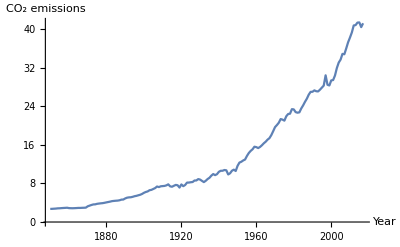

```mathematica
(* Plot of historical emissions *)
ListLinePlot[emissionsHis,LabelStyle->14,AxesLabel->{"Year","CO_2 emissions"}]
```

```mathematica
Total[emissionsHis[[;;,2]]]
```

2307.28

## Generate future projections using formulation from Raupach et al. (2014)

```mathematica
(* Parameters *)
quotaTot=2300; (* carbon quota *)
```

```mathematica
(* Create a 'business as usual' trajectory up to 2030 *)
emCurrent=emissionsHis[[-1]]; (* emissions data point for 2017 *)
busAsUsual={Range[emCurrent[[1]]+1,2030],ConstantArray[emCurrent[[2]],Length[Range[emCurrent[[1]]+1,2030]]]}//Transpose;
```

```mathematica
(* Join this onto the end of the historical emissions trajectory *)
emissionsHisExt=Join[emissionsHis,busAsUsual];
```

```mathematica
emissionsHisExt[[;;5]]//TableForm
```

1850 | 2.71801
1851 | 2.73254
1852 | 2.7616
1853 | 2.78794
1854 | 2.83469

```mathematica
(* compute quota available for the time period from year y0 onwards *)
Clear[quota]
quota[y0_]:=quotaTot-Total[emissionsHisExt[[1;;Position[emissionsHisExt[[;;,1]],y0][[1,1]],2]]];
```

```mathematica
(* Functional forms in terms of starting year to compute future emissions trajectory *)
Clear[f0,r]
(* Compute the emissions at the starting year y0 *)
f0[y0_]:=emissionsHisExt[[Position[emissionsHisExt[[;;,1]],y0][[1,1]],2]];
(* compute growth of emissions at starting year *)
r[y0_]:=(1/f0[y0]) (f0[y0+1]-f0[y0]); (* relative initial emission growth rate *)
```

```mathematica
quota[2017]
```

-7.27917

```mathematica
(* Find year where emissions first use up quota *)
i=2017;
While[quota[i]>0,i++];
quotaFullYear=i;
```

```mathematica
(* mitigation rate to achieve quota *)
Clear[m]
m[y0_]:=(1+Sqrt[1+r[y0] quota[y0] / f0[y0]])/(quota[y0] / f0[y0]);
```

```mathematica
Clear[emissionsFut]
emissionsFut[t_,y0_]:=f0[y0](1+(r[y0]+m[y0])(t-y0))Exp[-m[y0] (t-y0)];
```

```mathematica
(* choose a starting year *)
y0=2016;
```

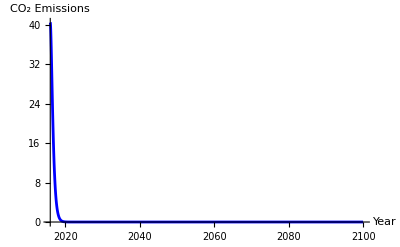

```mathematica
(* plot of future emission trajectory *)
Plot[emissionsFut[t,y0],{t,y0,2100},
LabelStyle->14,
PlotRange->All,
AxesLabel->{"Year","CO_2 Emissions"},
PlotStyle->{Blue,Thickness[0.005]}]
```

## Combine historical and future plots

```mathematica
tPlotMax=2100;
```

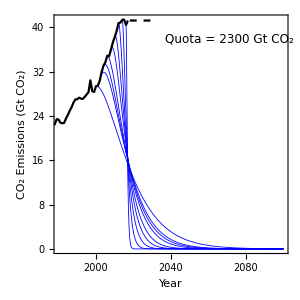

```mathematica
emissionsTrajPlot=Show[
(* future emissions from times preceding and including 2017 *)
Table[
Plot[emissionsFut[t,y0],{t,y0,tPlotMax},
LabelStyle->14,
PlotStyle->{Blue,Thickness[0.002]},
PlotRange->{{1980,2100},All}],
{y0,Range[2000,2017,2]}],
(* future emissions from times after 2017 up to time where quota runs out *)
Table[
Plot[emissionsFut[t,y0],{t,y0,tPlotMax},
LabelStyle->14,
AxesLabel->{"Year","CO_2 Emissions"},
PlotStyle->{Red,Thickness[0.002]},
PlotRange->{{1980,2100},All}],
{y0,Range[2018,quotaFullYear-1,2]}],
(* historical values up to 2017 *)
ListLinePlot[emissionsHis,
PlotRange->{{1980,tPlotMax},All},
PlotStyle->Black],
(* extended business as usual scenario *)
ListLinePlot[busAsUsual[[;;-2]],
PlotRange->{{1980,tPlotMax},All},
PlotStyle->{Black,Dashed}],
AspectRatio->1,
LabelStyle->14,
Ticks->{Range[1980,tPlotMax,20],Automatic},
AxesOrigin->{1980,0},
Frame->True,
FrameLabel->{{"CO_2 Emissions (Gt CO_2)",None},{"Year",None}},
Epilog->Text[Style["Quota = "<>ToString[quotaTot]<>" Gt CO_2",12],Scaled[{0.75,0.9}]],
ImageSize->300
]
```

```mathematica
(*Export["figures/emissions_quota_2300.png",emissionsTrajPlot,ImageResolution->100];*)
```